# Kerr geodesics

## Definitions

```mathematica
ClearAll[r,H,l,lx,ly,lz];
l[x_,y_,z_]:={1,lx[x,y,z],ly[x,y,z],lz[x,y,z]};

ClearAll[η];
η=DiagonalMatrix[{-1,1,1,1}];

ClearAll[llg];
llg=η+Table[2*H[x[λ],y[λ],z[λ]]l[x[λ],y[λ],z[λ]]⟦i⟧l[x[λ],y[λ],z[λ]]⟦j⟧,{i,1,4},{j,1,4}];

ClearAll[llγ,uuγ];
llγ=llg⟦2;;4,2;;4⟧;
uuγ=Inverse[llγ];

ClearAll[α];
α=FullSimplify[1/(√(1+2H[x[λ],y[λ],z[λ]](l[x[λ],y[λ],z[λ]]⟦1⟧)^2))];

ClearAll[lβ,uβ];
lβ=2H[x[λ],y[λ],z[λ]]l[x[λ],y[λ],z[λ]]⟦1⟧*{l[x[λ],y[λ],z[λ]]⟦2⟧,l[x[λ],y[λ],z[λ]]⟦3⟧,l[x[λ],y[λ],z[λ]]⟦4⟧};
uβ=Table[Sum[uuγ⟦i,j⟧lβ⟦j⟧,{j,1,3}],{i,1,3}];

ClearAll[coords];
coords={t[λ],x[λ],y[λ],z[λ]};

ClearAll[ℒ];
ℒ=Collect[Sum[1/2 llg⟦i,j⟧D[coords⟦i⟧,λ]D[coords⟦j⟧,λ],{i,1,4},{j,1,4}],Join[D[coords,λ],D[coords,{λ,2}]],FullSimplify];

ClearAll[EnKS];
EnKS=FullSimplify[-D[ℒ,t'[λ]]];

ClearAll[conservedKS];
conservedKS=FullSimplify[Flatten[Solve[EnKS==En,t'[λ]]]];
conservedKS=Join[conservedKS,FullSimplify[D[conservedKS,λ]]];

ClearAll[ELKS];
ELKS={
Collect[(D[D[ℒ,x'[λ]],λ]-D[ℒ,x[λ]])//.conservedKS,Join[D[coords,λ],D[coords,{λ,2}]],FullSimplify]==0,
Collect[(D[D[ℒ,y'[λ]],λ]-D[ℒ,y[λ]])//.conservedKS,Join[D[coords,λ],D[coords,{λ,2}]],FullSimplify]==0,
Collect[(D[D[ℒ,z'[λ]],λ]-D[ℒ,z[λ]])//.conservedKS,Join[D[coords,λ],D[coords,{λ,2}]],FullSimplify]==0
};

ClearAll[r,H,lx,ly,lz];
r[x_,y_,z_]:=√(1/2(x^2+y^2+z^2-a^2)+√(1/4(x^2+y^2+z^2-a^2)^2+a^2 z^2));
H[x_,y_,z_]:=(M*r[x,y,z]^3)/(r[x,y,z]^4+a^2*z^2);

lx[x_,y_,z_]:=(r[x,y,z]*x+a*y)/(r[x,y,z]^2+a^2)
ly[x_,y_,z_]:=(r[x,y,z]*y-a*x)/(r[x,y,z]^2+a^2)
lz[x_,y_,z_]:=z/r[x,y,z];
```

## Solver Function

```mathematica
ClearAll[solveGeodesic];
solveGeodesic[BHParams_,EnergyCondition_,InitPos_,InitVel_,LambdaParams_]:=Module[
{
Mass=BHParams⟦1⟧,
Spin=BHParams⟦2⟧,

x0=InitPos⟦1⟧,
y0=InitPos⟦2⟧,
z0=InitPos⟦3⟧,

vx0=InitVel⟦1⟧,
vy0=InitVel⟦2⟧,
vz0=InitVel⟦3⟧,

λ0=LambdaParams⟦1⟧,
λf=LambdaParams⟦2⟧,

norm,
EnSol,
eqs,
sol
},

If[(Mass^2-Spin^2)<0,
Print["Unphysical configuration (black hole)"];
Return[{}];
];

norm=Sum[llg⟦i,j⟧D[coords⟦i⟧,λ]D[coords⟦j⟧,λ],{i,1,4},{j,1,4}];
norm=norm//.conservedKS;
norm=norm//.{x[λ]->x0,y[λ]->y0,z[λ]->z0,x'[λ]->vx0,y'[λ]->vy0,z'[λ]->vz0,M->Mass,a->Spin};

EnSol=Flatten[Solve[{norm==-1,EnergyCondition},En,Reals]];

If[Length[EnSol]==0,
Print["Unphysical energy"];
Abort[];
];

eqs=Join[ELKS,{x[0]==x0,y[0]==y0,z[0]==z0,x'[0]==vx0,y'[0]==vy0,z'[0]==vz0}];
eqs=eqs//.{M->Mass,a->Spin};
eqs=eqs//.EnSol;

Off[NDSolve::ndsz,NDSolve::ndstf,NDSolve::mxst];
sol=Flatten[NDSolve[eqs,{x,y,z},{λ,λ0,λf},Method->{"Automatic","EquationSimplification"->"Residual"},AccuracyGoal->12,PrecisionGoal->12,MaxSteps->10^4]];
On[NDSolve::ndsz,NDSolve::ndstf,NDSolve::mxst];

Return[sol];
];
```

## Plotter function

```mathematica
ClearAll[plotGeodesic];
plotGeodesic[BHParams_,EnergyCondition_,InitPos_,InitVel_,LambdaParams_,PlotRadius_]:=Module[
{
Mass=BHParams⟦1⟧,
Spin=BHParams⟦2⟧,

ergosphere,
horizon,

sol,Λ0,Λf,
trajectory
},

ergosphere=ContourPlot[
(llg⟦1,1⟧//.{M->Mass,a->Spin}/.{x[λ]->x,y[λ]->y,z[λ]->0})==0,

{x,-PlotRadius,PlotRadius},
{y,-PlotRadius,PlotRadius},

ContourShading->False,
ContourStyle->Directive[Black,Thick,Dashed],
PlotRange->Full
];

horizon=ContourPlot[
(r[x,y,0]//.a->Spin)==(Mass+√(Mass^2-Spin^2)),

{x,-PlotRadius,PlotRadius},
{y,-PlotRadius,PlotRadius},

ContourShading->False,
ContourStyle->Directive[Black,Thick],
PlotRange->Full
];

sol=solveGeodesic[BHParams,EnergyCondition,InitPos,InitVel,LambdaParams];
{Λ0,Λf}=Flatten[x["Domain"]/.sol];

trajectory=ParametricPlot[
{x[λ]//.sol,y[λ]//.sol},
{λ,Λ0,Λf},

PlotStyle->Directive[Red,Thick],
PlotRange->Full
];

Show[
ergosphere,
horizon,
trajectory,

Axes->False,
Frame->True,
PlotRange->{{-PlotRadius,PlotRadius},{-PlotRadius,PlotRadius}}
]
];
```

## Transform

```mathematica
ClearAll[transform];
transform[BHParams_,EnergyCondition_,InitPos_,InitVel_,Plottable_:False,ArgToReturn_:1]:=Module[
{
Mass=BHParams⟦1⟧,
Spin=BHParams⟦2⟧,

x0=InitPos⟦1⟧,
y0=InitPos⟦2⟧,
z0=InitPos⟦3⟧,

vx0=InitVel⟦1⟧,
vy0=InitVel⟦2⟧,
vz0=InitVel⟦3⟧,

norm,EnSol,
dtdλ,dxdt,dydt,dzdt,
V,El
},
If[(Mass^2-Spin^2)<0,
If[Plottable==False,
Print["Unphysical configuration (black hole)"];
Abort[];
,
Return[Undefined];
]
];

norm=Sum[llg⟦i,j⟧D[coords⟦i⟧,λ]D[coords⟦j⟧,λ],{i,1,4},{j,1,4}];
norm=norm//.conservedKS;
norm=norm//.{x[λ]->x0,y[λ]->y0,z[λ]->z0,x'[λ]->vx0,y'[λ]->vy0,z'[λ]->vz0,M->Mass,a->Spin};

EnSol=Flatten[Solve[{norm==-1,EnergyCondition},En,Reals]];

If[Length[EnSol]==0,
If[Plottable==False,
Print["Unphysical energy"];
Abort[];
,
Return[Undefined];
]
];

If[Plottable==False,
Print["En = ",N[En//.EnSol,16]];
];

dtdλ=t'[λ]//.conservedKS//.{x[λ]->x0,y[λ]->y0,z[λ]->z0,x'[λ]->vx0,y'[λ]->vy0,z'[λ]->vz0,M->Mass,a->Spin}//.EnSol;
dxdt=vx0/dtdλ;
dydt=vy0/dtdλ;
dzdt=vz0/dtdλ;

V={(dxdt+uβ⟦1⟧)/α,(dydt+uβ⟦2⟧)/α,(dzdt+uβ⟦3⟧)/α};
V=V//.{x[λ]->x0,y[λ]->y0,z[λ]->z0,x'[λ]->vx0,y'[λ]->vy0,z'[λ]->vz0,M->Mass,a->Spin};

El=En/(α-Sum[llγ⟦i,j⟧uβ⟦i⟧V⟦j⟧,{i,1,3},{j,1,3}]);
El=El//.EnSol//.{x[λ]->x0,y[λ]->y0,z[λ]->z0,x'[λ]->vx0,y'[λ]->vy0,z'[λ]->vz0,M->Mass,a->Spin};

If[Plottable==False,
Return[
"initial_V1: "<>ToString[N[V⟦1⟧,16]]<>"\n"<>
"initial_V2: "<>ToString[N[V⟦2⟧,16]]<>"\n"<>
"initial_V3: "<>ToString[N[V⟦3⟧,16]]<>"\n"<>
"\n"<>
"initial_X1: "<>ToString[N[x0,16]]<>"\n"<>
"initial_X2: "<>ToString[N[y0,16]]<>"\n"<>
"initial_X3: "<>ToString[N[z0,16]]<>"\n"<>
"\n"<>
"initial_EN: "<>ToString[N[El,16]]
];
,
Return[Join[V,{x0,y0,z0,El}]⟦ArgToReturn⟧];
];
];
```

## Test

En = 3.633021323890078

initial_V1: 0.6824461505406538
initial_V2: 0.6634997977574913
initial_V3: 0

initial_X1: 1.000000000000000
initial_X2: 0
initial_X3: 0

initial_EN: 9.741128992908843

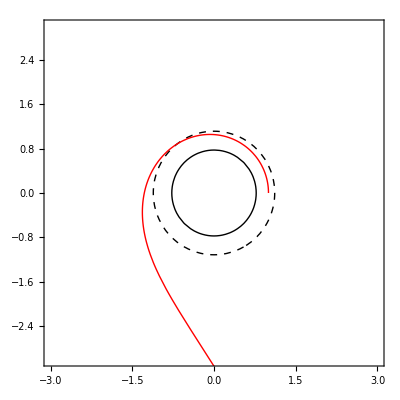

```mathematica
Block[
{M,a,x0,y0,z0,vx0,vy0,vz0,λ0,λf,R},
M=1/2;
a=98/100*M;

x0=1;
y0=0;
z0=0;

vx0=0;
vy0=102/10;
vz0=0;

λ0=0;
λf=10;

R=3;

Print[transform[{M,a},En>0,{x0,y0,z0},{vx0,vy0,vz0}]];
plotGeodesic[{M,a},En>0,{x0,y0,z0},{vx0,vy0,vz0},{λ0,λf},R]
]
```